```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 699 Kb

{Utilities`CleanSlate`,TriangleLink`,Parallel`Debug`Perfmon`,Parallel`Debug`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
Clear[zReplace]
zReplace = { 
z[t] -> x[t]^2/a
} ;
zReplace
```

{z[t]→x[t]^2/a}

```mathematica
D[zReplace, t]
```

{z'[t]→(2 x[t] x'[t])/a}

```mathematica
1/2 m ( x'[t]^2 + z'[t]^2 )
```

1/2 m (x'[t]^2+z'[t]^2)

```mathematica
1/2 m ( x'[t]^2 + z'[t]^2 )  /. D[zReplace, t]  // Expand // Simplify
```

(m (a^2+4 x[t]^2) x'[t]^2)/(2 a^2)

```mathematica
Clear[T] 
T = 
1/2 m ( x'[t]^2 + z'[t]^2 )  /. D[zReplace, t]  // Expand // Simplify
```

(m (a^2+4 x[t]^2) x'[t]^2)/(2 a^2)

```mathematica
m g z[t] 
m g z[t] /. zReplace
```

g m z[t]

(g m x[t]^2)/a

```mathematica
Clear[V]
V = m g z[t] /. zReplace
```

(g m x[t]^2)/a

```mathematica
Clear[ℒ]
ℒ = T - V
```

-(g m x[t]^2)/a+(m (a^2+4 x[t]^2) x'[t]^2)/(2 a^2)

```mathematica
Clear[q]
q = x[t]
```

x[t]

```mathematica
D[ D[ ℒ , D[q, t] ], t] - D[ ℒ , q ]
```

(2 g m x[t])/a+(4 m x[t] x'[t]^2)/a^2+(m (a^2+4 x[t]^2) x''[t])/a^2

```mathematica
Clear[eqs]
eqs = EulerEquations[ ℒ , q , t ]
```

-(m (2 x[t] (a g+2 x'[t]^2)+a^2 x''[t]+4 x[t]^2 x''[t]))/a^2==0

```mathematica
Clear[parameters]
parameters = { 
m -> 20 , 
a -> 50 , 
g-> 9.8
} ; 
parameters // TableForm
```

m→20
a→50
g→9.8

```mathematica
eqs /. parameters  // Expand
```

-7.84 x[t]-4/125 x[t] x'[t]^2-20 x''[t]-4/125 x[t]^2 x''[t]==0

```mathematica
Clear[ics]
ics = { 
x[0] == 2 , 
x'[0] == 0.5
} ;
ics // TableForm
```

x[0]==2
x'[0]==0.5

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ { eqs  } /. parameters , ics ] ,  q   , { t, 0, 300 } ] ]
```

{x[t]→InterpolatingFunction[…][t]}

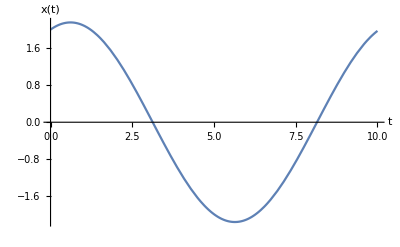

```mathematica
Plot[ Evaluate[ x[t] /. solution[t] ] , { t, 0, 10 } , AxesLabel-> { t, q }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 0.01 ,30  } ]
```